```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook];SetDirectory[NotebookDirectory[]];
```

## 1. Set up parameters

### 1.1 read input parameters H_0, Ω_b0, Ω_c0, T_CMB, n_s, α, q_0, (Ṽ)_1

```mathematica
inputdata=Import["bumblebee_input_data.txt","Table"]
```

{{70},{0.05},{0.25},{2.7},{1.},{-1.1},{-0.5},{1.2}}

```mathematica
{inputH0,inputOmb0,inputOmc0,inputTcmb,inputns}={inputdata[[1]][[1]],inputdata[[2]][[1]],inputdata[[3]][[1]],inputdata[[4]][[1]],inputdata[[5]][[1]]};
```

```mathematica
{inputal,inputq0,inputtilv1}={inputdata[[6]][[1]],inputdata[[7]][[1]],inputdata[[8]][[1]]};
```

### 1.2 constants and derived quantities

```mathematica
n=4;coord={et,r,th,ph};ccoord={et,x,y,z};
```

```mathematica
mesi=9.1093837015*10^-31;mpsi=1.67262192369*10^-27;mhsi=1.673575*10^-27;Gconsi=6.67430*10^-11;cconsi=299792458;kbconsi=1.380649*10^-23;hconsi=6.62607015*10^-34;econsi=1.602176634*10^-19;ep0consi=8.85418782*10^-12;
```

```mathematica
hbarconsi=hconsi/(2*Pi);alconsi=econsi^2/(4*Pi*ep0consi*hbarconsi*cconsi);hye0si=mesi/(2*hbarconsi^2)*(econsi^2/(4*Pi*ep0consi))^2;sitsi=(8*Pi)/3*(econsi^2/(4*Pi*ep0consi*mesi*cconsi^2))^2;sisbsi=(Pi^2*kbconsi^4)/(60*hbarconsi^3*cconsi^2);
```

```mathematica
megeo=(Gconsi*mesi)/cconsi^2;mpgeo=(Gconsi*mpsi)/cconsi^2;mhgeo=(Gconsi*mhsi)/cconsi^2;sitgeo=sitsi;
```

```mathematica
pgnum1=15;pgnum2=10;pgnum3=8;zeronum=10^-80;errornum1=10^-3;errornum2=10^-2;errornum3=10^-9;
```

```mathematica
H0si=inputH0*1000/(3.08567758128*10^16*10^6);Tcmb=inputTcmb;Omb0num=inputOmb0;Omc0num=inputOmc0;Omga0num=(8*Pi*Gconsi)/(3*H0si^2*cconsi^2)*(8*Pi^5*kbconsi^4)/(15*hconsi^3*cconsi^3)*(Tcmb)^4;Omla0num=1-Omb0num-Omc0num-Omga0num;{Omga0num,Omla0num}
```

{0.0000486065,0.699951}

```mathematica
H0geo=H0si*1/cconsi;menum=megeo*H0geo;mpnum=mpgeo*H0geo;mhnum=mhgeo*H0geo;sitnum=sitsi*H0geo^2
```

3.80922×10^-81

```mathematica
nsnum=inputns;decalrsq=k^(nsnum-1);
```

```mathematica
kanum=8*Pi;H0num=1;{lnaini,lnaend}={-14,0};aininum=N[Exp[lnaini]];numrep0={H0->H0num,ka->kanum,Omb0->Omb0num,Omc0->Omc0num,Omga0->Omga0num,Omla0->0};
```

```mathematica
alnum=inputal;xitnum=-(2 (2+al))/(al+2 q0)/.{al->alnum,q0->inputq0};xi2tnum=-(al xit)/(2 (2+al))/.{al->alnum,xit->xitnum};v1tnum=38;v1num=v1tnum*(3*H0num^2)/kanum;numrep1={xi->xitnum*v1tnum,xi2->xi2tnum*v1tnum,v1->v1num,xit->xitnum,xi2t->xi2tnum,v1t->v1tnum,al->alnum};
```

## 2. Calculate field equation

### 2.1 curvature quantities

```mathematica
scalarpertfuns={bps[et,x,y,z]->bps[et]*Exp[I*(kx*x+ky*y+kz*z)],bph[et,x,y,z]->bph[et]*Exp[I*(kx*x+ky*y+kz*z)],deugax[et,x,y,z]->D[(-3*bth1[et])/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],x],deugay[et,x,y,z]->D[(-3*bth1[et])/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],y],deugaz[et,x,y,z]->D[(-3*bth1[et])/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],z],bpigaxx[et,x,y,z]->2/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],x,x]-1/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],y,y]-1/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],z,z],bpigayy[et,x,y,z]->2/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],y,y]-1/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],x,x]-1/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],z,z],bpigazz[et,x,y,z]->2/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],z,z]-1/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],y,y]-1/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],x,x],bpigaxy[et,x,y,z]->D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],x,y],bpigaxz[et,x,y,z]->D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],x,z],bpigayz[et,x,y,z]->D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],z,y],deepga[et,x,y,z]->4*epga[et]*bth0[et]*Exp[I*(kx*x+ky*y+kz*z)],deubx[et,x,y,z]->D[vb[et]/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],x],deuby[et,x,y,z]->D[vb[et]/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],y],deubz[et,x,y,z]->D[vb[et]/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],z],deepb[et,x,y,z]->epb[et]*deb[et]*Exp[I*(kx*x+ky*y+kz*z)],deucx[et,x,y,z]->D[vc[et]/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],x],deucy[et,x,y,z]->D[vc[et]/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],y],deucz[et,x,y,z]->D[vc[et]/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],z],deepc[et,x,y,z]->epc[et]*dec[et]*Exp[I*(kx*x+ky*y+kz*z)],debt[et,x,y,z]->debt[et]*Exp[I*(kx*x+ky*y+kz*z)],debx[et,x,y,z]->D[debs[et]/Sqrt[kx^2+ky^2+kz^2]*Exp[I*(kx*x+ky*y+kz*z)],x],deby[et,x,y,z]->D[debs[et]/Sqrt[kx^2+ky^2+kz^2]*Exp[I*(kx*x+ky*y+kz*z)],y],debz[et,x,y,z]->D[debs[et]/Sqrt[kx^2+ky^2+kz^2]*Exp[I*(kx*x+ky*y+kz*z)],z]};
```

```mathematica
metric1=(af[et])^2*{{0,0,0,0},{0,1/(1+Omk0*H0^2*r^2),0,0},{0,0,r^2,0},{0,0,0,r^2*(Sin[th])^2}};metricet={{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};metricetsph={{-1,0,0,0},{0,1,0,0},{0,0,r^2,0},{0,0,0,r^2*(Sin[th])^2}};ctran={et,r*Sin[th]*Cos[ph],r*Sin[th]*Sin[ph],r*Cos[th]};jmet=Table[D[ctran[[i]],coord[[j]]],{i,1,n},{j,1,n}];jmetinv=Simplify[Inverse[jmet]];cmetric1=Simplify[Transpose[jmetinv].metric1.jmetinv/.{Cos[th]->z/r,Sin[th]->Sqrt[x^2+y^2]/r,Cos[ph]->x/Sqrt[x^2+y^2],Sin[ph]->y/Sqrt[x^2+y^2]}/.r->Sqrt[x^2+y^2+z^2]];cmetric=af[et]^2*(1+po*2*bps[et,x,y,z])*{{-1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}+(1-po*2*bph[et,x,y,z])*cmetric1/.Omk0->0/.scalarpertfuns;
```

```mathematica
AbsoluteTiming[poord=1;inversecmetric=Normal[Series[Inverse[cmetric],{po,0,poord}]];chris=Normal[Series[Table[(1/2)*Sum[inversecmetric[[i,s]]*(D[cmetric[[s,k]],ccoord[[j]]]+D[cmetric[[j,s]],ccoord[[k]]]-D[cmetric[[j,k]],ccoord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}],{po,0,poord}]];riemann=Normal[Series[Table[D[chris[[i,j,ll]],ccoord[[k]]]-D[chris[[i,j,k]],ccoord[[ll]]]+Sum[chris[[i,k,s]]*chris[[s,ll,j]]-chris[[i,ll,s]]*chris[[s,k,j]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{ll,1,n}],{po,0,poord}]];ricci=Table[Sum[riemann[[s,j,s,k]],{s,1,n}],{j,1,n},{k,1,n}];riccis=Normal[Series[Sum[inversecmetric[[i,j]]*ricci[[i,j]],{i,1,n},{j,1,n}],{po,0,poord}]];einstein=Normal[Series[Table[ricci[[i,j]]-1/2*cmetric[[i,j]]*riccis,{i,1,n},{j,1,n}],{po,0,poord}]];]
```

{0.896924,Null}

### 2.2 bumblebee contribution

```mathematica
AbsoluteTiming[bdown={af[et]*btf[et],0,0,0}+po*af[et]*{debt[et,x,y,z],debx[et,x,y,z],deby[et,x,y,z],debz[et,x,y,z]}/.scalarpertfuns;bsq=Normal[Series[Sum[inversecmetric[[i,j]]*bdown[[i]]*bdown[[j]],{i,1,n},{j,1,n}],{po,0,poord}]];bbdown=Table[bdown[[i]]*bdown[[j]],{i,1,n},{j,1,n}];db=Table[D[bdown[[j]],ccoord[[i]]]-Sum[chris[[s1,i,j]]*bdown[[s1]],{s1,1,n}],{i,1,n},{j,1,n}];bten=Table[db[[i,j]]-db[[j,i]],{i,1,n},{j,1,n}];dbb=Table[D[bbdown[[j,k]],ccoord[[i]]]-Sum[chris[[s1,i,j]]*bbdown[[s1,k]]+chris[[s1,i,k]]*bbdown[[j,s1]],{s1,1,n}],{i,1,n},{j,1,n},{k,1,n}];ddbb=Table[D[dbb[[i2,i3,i4]],ccoord[[i1]]]-Sum[chris[[s1,i1,i2]]*dbb[[s1,i3,i4]]+chris[[s1,i1,i3]]*dbb[[i2,s1,i4]]+chris[[s1,i1,i4]]*dbb[[i2,i3,s1]],{s1,1,n}],{i1,1,n},{i2,1,n},{i3,1,n},{i4,1,n}];tbdown=Normal[Series[Table[xi*(1/2*cmetric[[i,j]]*Sum[inversecmetric[[s1,s3]]*inversecmetric[[s2,s4]]*bbdown[[s1,s2]]*ricci[[s3,s4]],{s1,1,n},{s2,1,n},{s3,1,n},{s4,1,n}]-Sum[inversecmetric[[s1,s2]]*bbdown[[i,s1]]*ricci[[j,s2]]+inversecmetric[[s1,s2]]*bbdown[[j,s1]]*ricci[[i,s2]],{s1,1,n},{s2,1,n}]+1/2*(Sum[inversecmetric[[s1,s2]]*ddbb[[s1,i,s2,j]]+inversecmetric[[s1,s2]]*ddbb[[s1,j,s2,i]]-inversecmetric[[s1,s2]]*ddbb[[s1,s2,i,j]],{s1,1,n},{s2,1,n}]-cmetric[[i,j]]*Sum[inversecmetric[[s1,s3]]*inversecmetric[[s2,s4]]*ddbb[[s1,s2,s3,s4]],{s1,1,n},{s2,1,n},{s3,1,n},{s4,1,n}]))+ka*(Sum[inversecmetric[[s1,s2]]*bten[[i,s1]]*bten[[j,s2]],{s1,1,n},{s2,1,n}]-1/4*cmetric[[i,j]]*Sum[inversecmetric[[s1,s3]]*inversecmetric[[s2,s4]]*bten[[s1,s2]]*bten[[s3,s4]],{s1,1,n},{s2,1,n},{s3,1,n},{s4,1,n}]-bv*cmetric[[i,j]]+2*bbdown[[i,j]]*bvp)+xi2*(-bsq*einstein[[i,j]]-bdown[[i]]*bdown[[j]]*riccis+Sum[ddbb[[i,j,i1,i2]]*inversecmetric[[i1,i2]],{i1,1,n},{i2,1,n}]-cmetric[[i,j]]*Sum[ddbb[[i1,i2,i3,i4]]*inversecmetric[[i1,i2]]*inversecmetric[[i3,i4]],{i1,1,n},{i2,1,n},{i3,1,n},{i4,1,n}])/.{bv->v1*bsq,bvp->v1},{i,1,n},{j,1,n}],{po,0,poord}]];]
```

{10.3514,Null}

### 2.3 photon energy-momentum tensor

```mathematica
ugaup={1/af[et],0,0,0}+po*{-1/af[et]*bps[et,x,y,z],deugax[et,x,y,z],deugay[et,x,y,z],deugaz[et,x,y,z]}/.scalarpertfuns;ugadown=Normal[Series[Table[Sum[cmetric[[i,i1]]*ugaup[[i1]],{i1,1,n}],{i,1,n}],{po,0,poord}]];tfgamn=Normal[Series[Table[(ep+p)*ugadown[[i]]*ugadown[[j]]+p*cmetric[[i,j]],{i,1,n},{j,1,n}]/.{ep->epga[et]+po*deepga[et,x,y,z],p->1/3*(epga[et]+po*deepga[et,x,y,z])},{po,0,poord}]]+po*{{0,0,0,0},{0,bpigaxx[et,x,y,z],bpigaxy[et,x,y,z],bpigaxz[et,x,y,z]},{0,bpigaxy[et,x,y,z],bpigayy[et,x,y,z],bpigayz[et,x,y,z]},{0,bpigaxz[et,x,y,z],bpigayz[et,x,y,z],bpigazz[et,x,y,z]}}/.scalarpertfuns;tfgamnup=Normal[Series[Table[Sum[tfgamn[[i1,i2]]*inversecmetric[[i,i1]]*inversecmetric[[j,i2]],{i1,1,n},{i2,1,n}],{i,1,n},{j,1,n}],{po,0,poord}]];tfgamncon=Normal[Series[Table[Sum[D[tfgamnup[[i1,i]],ccoord[[i1]]],{i1,1,n}]+Sum[chris[[i1,i1,i2]]*tfgamnup[[i2,i]]+chris[[i,i1,i2]]*tfgamnup[[i1,i2]],{i1,1,n},{i2,1,n}],{i,1,n}],{po,0,poord}]];
```

### 2.4 baryon energy-momentum tensor

```mathematica
ubup={1/af[et],0,0,0}+po*{-1/af[et]*bps[et,x,y,z],deubx[et,x,y,z],deuby[et,x,y,z],deubz[et,x,y,z]}/.scalarpertfuns;ubdown=Normal[Series[Table[Sum[cmetric[[i,i1]]*ubup[[i1]],{i1,1,n}],{i,1,n}],{po,0,poord}]];tfbmn=Normal[Series[Table[(ep+p)*ubdown[[i]]*ubdown[[j]]+p*cmetric[[i,j]],{i,1,n},{j,1,n}]/.{ep->epb[et]+po*deepb[et,x,y,z],p->0},{po,0,poord}]]/.scalarpertfuns;tfbmnup=Normal[Series[Table[Sum[tfbmn[[i1,i2]]*inversecmetric[[i,i1]]*inversecmetric[[j,i2]],{i1,1,n},{i2,1,n}],{i,1,n},{j,1,n}],{po,0,poord}]];tfbmncon=Normal[Series[Table[Sum[D[tfbmnup[[i1,i]],ccoord[[i1]]],{i1,1,n}]+Sum[chris[[i1,i1,i2]]*tfbmnup[[i2,i]]+chris[[i,i1,i2]]*tfbmnup[[i1,i2]],{i1,1,n},{i2,1,n}],{i,1,n}],{po,0,poord}]];
```

### 2.5 cold dark matter energy-momentum tensor

```mathematica
ucup={1/af[et],0,0,0}+po*{-1/af[et]*bps[et,x,y,z],deucx[et,x,y,z],deucy[et,x,y,z],deucz[et,x,y,z]}/.scalarpertfuns;ucdown=Normal[Series[Table[Sum[cmetric[[i,i1]]*ucup[[i1]],{i1,1,n}],{i,1,n}],{po,0,poord}]];tfcmn=Normal[Series[Table[(ep+p)*ucdown[[i]]*ucdown[[j]]+p*cmetric[[i,j]],{i,1,n},{j,1,n}]/.{ep->epc[et]+po*deepc[et,x,y,z],p->0},{po,0,poord}]]/.scalarpertfuns;tfcmnup=Normal[Series[Table[Sum[tfcmn[[i1,i2]]*inversecmetric[[i,i1]]*inversecmetric[[j,i2]],{i1,1,n},{i2,1,n}],{i,1,n},{j,1,n}],{po,0,poord}]];tfcmncon=Normal[Series[Table[Sum[D[tfcmnup[[i1,i]],ccoord[[i1]]],{i1,1,n}]+Sum[chris[[i1,i1,i2]]*tfcmnup[[i2,i]]+chris[[i,i1,i2]]*tfcmnup[[i1,i2]],{i1,1,n},{i2,1,n}],{i,1,n}],{po,0,poord}]];
```

### 2.6 Einstein field equations

```mathematica
eeq=einstein-ka*tfmn-ka*tfcmn-tbdown+bla*cmetric/.bla->3 H0^2 Omla0;
```

### 2.7 vector field equation

```mathematica
veceq=Normal[Series[Table[Sum[inversecmetric[[s1,s2]]*D[bten[[s2,i]],ccoord[[s1]]],{s1,1,n},{s2,1,n}]-Sum[inversecmetric[[s2,s3]]*(chris[[s1,s2,s3]]*bten[[s1,i]]+chris[[s1,s2,i]]*bten[[s3,s1]]),{s1,1,n},{s2,1,n},{s3,1,n}]+xi/ka*Sum[inversecmetric[[s1,s2]]*bdown[[s1]]*ricci[[s2,i]],{s1,1,n},{s2,1,n}]+xi2/ka*bdown[[i]]*riccis-2*bvp*bdown[[i]]/.{bv->v1*bsq,bvp->v1},{i,1,n}],{po,0,poord}]];
```

### 2.8 Boltzmann equation and conservation equations

```mathematica
boltzeqset={bth0'[et]-(-k bth1[et]+bph'[et]),bth1'[et]-1/3 (k bps[et]+k bth0[et]-3 bga[et] bth1[et]-2 k bth2[et]-bga[et] vb[et]),9/10 bga[et] bth2[et]+1/5 k (-2 bth1[et]+3 bth3[et])+bth2'[et],deb'[et]-(k vb[et]+3 bph'[et]),vb'[et]-1/(3 af[et] epb[et])(-3 k af[et] bps[et] epb[et]-12 af[et] bga[et] bth1[et] epga[et]-4 af[et] bga[et] epga[et] vb[et]-3 epb[et] vb[et] af'[et]),dec'[et]-(k vc[et]+3 bph'[et]),vc'[et]-((-k af[et] bps[et]-vc[et] af'[et])/af[et])};
```

```mathematica
boltzeqhigh=bthl'[et]+k/(2*l+1)*((l+1)*bthlp1[et]-l*bthlm1[et])+bga[et]*(1-KroneckerDelta[l,2]/10)*bthl[et];
```

### 2.9 reduce the field equations and change variable: η→a

```mathematica
{epgasol,epbsol,epcsol}={(3*H0^2*Omga0)/(ka*(af[et])^4),(3*H0^2*Omb0)/(ka*(af[et])^3),(3*H0^2*Omc0)/(ka*(af[et])^3)};{epgasollna,epbsollna,epcsollna}={epgasol,epbsol,epcsol}/.{af[et]->Exp[lna]};{epgapsol,epbpsol,epcpsol}={(-4*af'[et]*epga[et])/af[et],(-3*af'[et]*epb[et])/af[et],(-3*af'[et]*epc[et])/af[et]};
```

```mathematica
appsol=-(-2 ka v1 af[et]^4-3 xi af'[et]^2)/(3 (xi+2 xi2) af[et]);btpsol=(ka v1 af[et]^4 btf[et]^2-ka af[et]^4 epb[et]-ka af[et]^4 epc[et]-ka af[et]^4 epga[et]+3 af'[et]^2-3 xi btf[et]^2 af'[et]^2-3 xi2 btf[et]^2 af'[et]^2)/(3 (xi+2 xi2) af[et] btf[et] af'[et]);btppsol=1/((xi+2 xi2) btf[et])(-1/(3 (xi+2 xi2) btf[et]^2)ka af[et]^2 (2 v1 (xi-xi2) btf[et]^4-2 (epb[et]+epc[et]+epga[et])-btf[et]^2 (xi epb[et]+xi epc[et]+2 (v1+(xi+xi2) epga[et])))-(ka^2 af[et]^6 (-v1 btf[et]^2+epb[et]+epc[et]+epga[et])^2)/(9 (xi+2 xi2) btf[et]^2 af'[et]^2)+((-1-2 xi2 btf[et]^2+(xi^2+4 xi xi2+3 xi2^2) btf[et]^4) af'[et]^2)/((xi+2 xi2) af[et]^2 btf[et]^2));
```

```mathematica
test1=Simplify[ⅇ^(-(ⅈ kx x+ⅈ ky y+ⅈ kz z))*Coefficient[eeq[[1,1]],po,1]];test2=Simplify[ⅇ^(-(ⅈ kx x+ⅈ ky y+ⅈ kz z))/kx*Coefficient[eeq[[1,2]],po,1]];test3=Simplify[ⅇ^(-(ⅈ kx x+ⅈ ky y+ⅈ kz z))/(kx*ky)*Coefficient[eeq[[2,3]],po,1]];test4=Simplify[ⅇ^(-(ⅈ kx x+ⅈ ky y+ⅈ kz z))*Coefficient[eeq[[3,3]],po,1]];{seleq11,seleq12,seleq13,seleq14}=Simplify[{test1,I*test2,test3,test4}/.{kx->0,ky->k,kz->0},Assumptions->k>0];
```

```mathematica
test1=Simplify[ⅇ^(-(ⅈ kx x+ⅈ ky y+ⅈ kz z))*Coefficient[veceq[[1]],po,1]];test2=Simplify[ⅇ^(-(ⅈ kx x+ⅈ ky y+ⅈ kz z))/kx*Coefficient[veceq[[2]],po,1]];{seleq15,seleq16}=Simplify[{test1,I*test2}/.{epb'[et]->epbpsol,epc'[et]->epcpsol,epga'[et]->epgapsol}/.{kx->k,ky->0,kz->0},Assumptions->k>0];
```

```mathematica
fieldeqset={seleq11,seleq12,seleq13,seleq14,seleq15,seleq16};
```

```mathematica
ettoa={af''[et]->a*calh[a]*(calh[a]+a*calh'[a]),af'[et]->a*calh[a],af[et]->a,btf[et]->btf[a],btf'[et]->a*calh[a]*btf'[a],btf''[et]->a*calh[a]*(btf''[a]*a*calh[a]+btf'[a]*calh[a]+btf'[a]*a*calh'[a]),bth0[et]->bth0[a],bth0'[et]->a*calh[a]*bth0'[a],bth0''[et]->a*calh[a]*(bth0''[a]*a*calh[a]+bth0'[a]*calh[a]+bth0'[a]*a*calh'[a]),bth1[et]->bth1[a],bth1'[et]->a*calh[a]*bth1'[a],bth1''[et]->a*calh[a]*(bth1''[a]*a*calh[a]+bth1'[a]*calh[a]+bth1'[a]*a*calh'[a]),bth2[et]->bth2[a],bth2'[et]->a*calh[a]*bth2'[a],bth2''[et]->a*calh[a]*(bth2''[a]*a*calh[a]+bth2'[a]*calh[a]+bth2'[a]*a*calh'[a]),bth3[et]->bth3[a],bth3'[et]->a*calh[a]*bth3'[a],bth3''[et]->a*calh[a]*(bth3''[a]*a*calh[a]+bth3'[a]*calh[a]+bth3'[a]*a*calh'[a]),bthl[et]->bthl[a],bthl'[et]->a*calh[a]*bthl'[a],bthlp1[et]->bthlp1[a],bthlm1[et]->bthlm1[a],bph[et]->bph[a],bph[et]->bph[a],bph'[et]->a*calh[a]*bph'[a],bph''[et]->a*calh[a]*(bph''[a]*a*calh[a]+bph'[a]*calh[a]+bph'[a]*a*calh'[a]),bps[et]->bps[a],bps'[et]->a*calh[a]*bps'[a],bps''[et]->a*calh[a]*(bps''[a]*a*calh[a]+bps'[a]*calh[a]+bps'[a]*a*calh'[a]),deb[et]->deb[a],deb'[et]->a*calh[a]*deb'[a],deb''[et]->a*calh[a]*(deb''[a]*a*calh[a]+deb'[a]*calh[a]+deb'[a]*a*calh'[a]),vb[et]->vb[a],vb'[et]->a*calh[a]*vb'[a],vb''[et]->a*calh[a]*(vb''[a]*a*calh[a]+vb'[a]*calh[a]+vb'[a]*a*calh'[a]),dec[et]->dec[a],dec'[et]->a*calh[a]*dec'[a],dec''[et]->a*calh[a]*(dec''[a]*a*calh[a]+dec'[a]*calh[a]+dec'[a]*a*calh'[a]),vc[et]->vc[a],vc'[et]->a*calh[a]*vc'[a],vc''[et]->a*calh[a]*(vc''[a]*a*calh[a]+vc'[a]*calh[a]+vc'[a]*a*calh'[a]),debt[et]->debt[a],debt'[et]->a*calh[a]*debt'[a],debt''[et]->a*calh[a]*(debt''[a]*a*calh[a]+debt'[a]*calh[a]+debt'[a]*a*calh'[a]),debs[et]->debs[a],debs'[et]->a*calh[a]*debs'[a],debs''[et]->a*calh[a]*(debs''[a]*a*calh[a]+debs'[a]*calh[a]+debs'[a]*a*calh'[a]),bga[et]->bga[a]};
```

```mathematica
testeq=af''[et]-appsol/.ettoa;calhsolap=calh'[a]/.Solve[testeq==0,calh'[a]][[1]];testeq=btf'[et]-btpsol/.{epga[et]->epgasol,epb[et]->epbsol,epc[et]->epcsol}/.ettoa;btsolap=Simplify[btf'[a]/.Solve[testeq==0,btf'[a]][[1]]];testeq=btf''[et]-btppsol/.{epga[et]->epgasol,epb[et]->epbsol,epc[et]->epcsol}/.ettoa;btsolapp=Simplify[btf''[a]/.Solve[testeq==0,btf''[a]][[1]]/.{btf'[a]->btsolap,calh'[a]->calhsolap}];
```

```mathematica
fieldeqseta=Simplify[fieldeqset/.{epga[et]->epgasol,epb[et]->epbsol,epc[et]->epcsol}/.ettoa];boltzeqseta=Simplify[boltzeqset/.{epga[et]->epgasol,epb[et]->epbsol,epc[et]->epcsol}/.ettoa];boltzeqhigha=boltzeqhigh/.ettoa;boltzhighsolp=bthl'[a]/.Solve[boltzeqhigha==0,bthl'[a]][[1]]//Simplify;
```

```mathematica
testsol2d=Solve[{fieldeqset[[1]]==0,fieldeqset[[4]]==0},{bph''[et],bps''[et]}];testeqset1=Simplify[fieldeqset/.testsol2d[[1]]];fieldeq4set={testeqset1[[2]],testeqset1[[3]],testeqset1[[5]],fieldeqset[[6]]};
```

```mathematica
AbsoluteTiming[fieldeq4seta=Simplify[fieldeq4set/.{af''[et]->appsol,btf''[et]->btppsol,btf'[et]->btpsol}/.{epga'[et]->epgapsol}/.{epga[et]->epgasol,epb[et]->epbsol,epc[et]->epcsol}/.ettoa/.{calh'[a]->calhsolap}];]
```

{0.36198,Null}

```mathematica
boltzeqaadd1=boltzeqhigha/.{l->3,bthlm1[a]->bth2[a],bthlp1[a]->bth4[a],bthl[a]->bth3[a],bthl'[a]->bth3'[a]};boltzeqaadd2=boltzeqhigha/.{l->4,bthlm1[a]->bth3[a],bthlp1[a]->bth5[a],bthl[a]->bth4[a],bthl'[a]->bth4'[a]};boltzsolp=Solve[{boltzeqseta[[1]]==0,boltzeqseta[[2]]==0,boltzeqseta[[3]]==0,boltzeqseta[[4]]==0,boltzeqseta[[5]]==0,boltzeqseta[[6]]==0,boltzeqseta[[7]]==0,boltzeqaadd1==0,boltzeqaadd2==0},{bth0'[a],bth1'[a],bth2'[a],deb'[a],dec'[a],vc'[a],vb'[a],bth3'[a],bth4'[a]}];
```

```mathematica
AbsoluteTiming[testsoldebsp=debs'[a]/.Solve[fieldeq4seta[[2]]==0,debs'[a]][[1]];testsoldebspp=Simplify[D[testsoldebsp,a]/.boltzsolp[[1]]/.{btf'[a]->btsolap,btf''[a]->btsolapp,calh'[a]->calhsolap}];testeqset1=fieldeq4seta/.{debs''[a]->testsoldebspp};testeqset1sol=Solve[{testeqset1[[1]]==0,testeqset1[[2]]==0,testeqset1[[3]]==0,testeqset1[[4]]==0},{bph'[a],bps'[a],debt'[a],debs'[a]}]//Simplify;fieldeq4setasol={bph'[a],bps'[a],debt'[a],debs'[a]}/.testeqset1sol[[1]];]
```

{3.45146,Null}

```mathematica
AbsoluteTiming[boln=20;boltztrseta=Simplify[Table[boltzeqhigha/.{l->ll,bthl[a]->bthf[a,ll],bthl'[a]->D[bthf[a,ll],a],bthlm1[a]->bthf[a,ll-1],bthlp1[a]->bthf[a,ll+1]}/.{calh[a]->calhsola}/.{bthf[a,boln+1]->(2*boln+1)/(k*etf[a])*bthf[a,boln]-bthf[a,boln-1]},{ll,1,boln}]];boltzhighsolptrset=Simplify[Table[boltzhighsolp/.{l->ll,bthl[a]->bthf[a,ll],bthl'[a]->D[bthf[a,ll],a],bthlm1[a]->bthf[a,ll-1],bthlp1[a]->bthf[a,ll+1]}/.{calh[a]->calhsola}/.{bthf[a,boln+1]->(2*boln+1)/(k*etf[a])*bthf[a,boln]-bthf[a,boln-1]},{ll,1,boln}]];]
```

{0.085966,Null}

```mathematica
boltzsolpbasic={deb'[a],dec'[a],vb'[a],vc'[a],bth0'[a],bth1'[a]}/.boltzsolp[[1]];fpsoltrset=Join[fieldeq4setasol/.{bth0[a]->bthf[a,0],bth1[a]->bthf[a,1],bth2[a]->bthf[a,2],bth3[a]->bthf[a,3]},boltzsolpbasic/.{bth0[a]->bthf[a,0],bth1[a]->bthf[a,1],bth2[a]->bthf[a,2],bth3[a]->bthf[a,3]},Table[boltzhighsolptrset[[i]],{i,2,boln}]];ftrset=Join[{bph[a],bps[a],debt[a],debs[a],deb[a],dec[a],vb[a],vc[a],bthf[a,0]},Table[bthf[a,i],{i,1,boln}]];fptrset=D[ftrset,a];
```

```mathematica
MatrixForm[fieldeq4set]
```

((ka af[et]^4 (2 v1 btf[et] debs[et]-epc[et] vc[et])+3 xi btf[et] debs[et] af'[et]^2+k af[et]^2 (2 (-1+(xi+xi2) btf[et]^2) bph'[et]+(xi+2 xi2) (btf[et]^2 bps'[et]-debt[et] btf'[et]+btf[et] (3 bps[et] btf'[et]-debt'[et])))+af[et] (k bps[et] (-2+3 xi btf[et]^2) af'[et]-btf[et] (k (xi-2 xi2) debt[et] af'[et]+3 (xi+2 xi2) debs[et] af''[et])))/(k af[et]^2)
(-2 xi btf[et] debs[et] af'[et]+af[et] (k bph[et] (-1+xi2 btf[et]^2)+bps[et] (k+k xi2 btf[et]^2)-2 k xi2 btf[et] debt[et]-xi debs[et] btf'[et]-xi btf[et] debs'[et]))/(k af[et])
(af[et]^4 (ka dec[et] epc[et]+2 bps[et] (3 H0^2 Omla0+ka epc[et]))+3 btf[et] (-2 (xi+xi2) bps[et] btf[et]+(3 xi+2 xi2) debt[et]) af'[et]^2-af[et]^2 (2 k^2 bph[et] (-1+xi2 btf[et]^2)+btf[et] (k^2 (xi+2 xi2) bps[et] btf[et]+k^2 (ka-xi-2 xi2) debt[et]+3 xi bph'[et] btf'[et]+6 xi2 bph'[et] btf'[et]-k ka debs'[et]))+af[et] (-3 btf[et]^2 af'[et] (2 (xi+xi2) bph'[et]+(xi+2 xi2) bps'[et])+3 af'[et] (2 bph'[et]+(xi+2 xi2) debt[et] btf'[et])+btf[et] (k (ka+2 xi) debs[et] af'[et]-3 (xi+2 xi2) (2 bps[et] af'[et] btf'[et]-af'[et] debt'[et]+debt[et] af''[et]))))/(ka af[et]^3 btf[et])
(2 ka v1 af[et]^4 debs[et]-xi debs[et] af'[et]^2+af[et] (2 k xi bps[et] btf[et] af'[et]-k ka debt[et] af'[et]+2 ka af'[et] debs'[et]+ka debs[et] af''[et]-xi debs[et] af''[et]-6 xi2 debs[et] af''[et])+af[et]^2 (2 k xi btf[et] bph'[et]+ka (-k debt'[et]+debs''[et])))/(k ka af[et]^3))

### 2.10 approximate solution at a→0

```mathematica
apphomobph=bph1*a^s1;apphomobps=bps1*a^s1;apphomodebt=debt1*a^(s1-1-al/4);apphomodebs=debs1*a^(s1-1-3*al/4);apphomoini={{s1->0,bps1->-((-2+al) bph1)/(2 (3+al)),debt1->-(3 al bph1 bt0)/(4 (3+al)),debs1->(bph1 bt0 k)/((3+al) H0 √((4-2 xit+al (2+xit))/((-2+al) xit)))},{s1->al,bps1->-1/2 (2+al) bph1,debt1->-1/4 al bph1 bt0,debs1->-(bph1 bt0 k)/(H0 √((4-2 xit+al (2+xit))/((-2+al) xit)))},{s1->(2 al ka+√(al^2 ka^2+32 ka v1t xit-16 al ka v1t xit))/(4 ka),bps1->-(bph1 (4 ka+√(ka (al^2 ka+32 v1t xit-16 al v1t xit))))/(4 ka),debt1->(bph1 bt0 (al ka-√(ka (al^2 ka+32 v1t xit-16 al v1t xit))))/(4 ka),debs1->-(al bph1 bt0 k)/(2 (2+al) H0 √((4-2 xit+al (2+xit))/((-2+al) xit)))},{s1->(2 al ka-√(al^2 ka^2+32 ka v1t xit-16 al ka v1t xit))/(4 ka),bps1->(bph1 (-4 ka+√(ka (al^2 ka+32 v1t xit-16 al v1t xit))))/(4 ka),debt1->(bph1 bt0 (al ka+√(ka (al^2 ka+32 v1t xit-16 al v1t xit))))/(4 ka),debs1->-(al bph1 bt0 k)/(2 (2+al) H0 √((4-2 xit+al (2+xit))/((-2+al) xit)))}};
```

```mathematica
appinhomoini={s1->-al/2,bph1->-((16 (-4+al^2) bth00 Omga0 (3 al (12+al) ka-16 (-2+al) xi))/(3 al (4+al) bt0^2 (2 (2+al) v1t+(-2+al) xi) (15 al^2 ka+16 (-2+al) xi))),bps1->-((16 (-2+al) (-1+al) (2+al) bth00 Omga0 (3 al (12+al) ka-16 (-2+al) xi))/(3 al (4+al) bt0^2 (2 (2+al) v1t+(-2+al) xi) (15 al^2 ka+16 (-2+al) xi))),debt1->(8 (-4+al^2) bth00 Omga0 (15 al^3 ka+32 (-2+al) (3+2 al) xi))/(3 al (4+al) bt0 (2 (2+al) v1t+(-2+al) xi) (15 al^2 ka+16 (-2+al) xi)),debs1->-((32 (-4+al^2) bth00 k Omga0 (3 al^2 ka+8 (-2+al) xi))/(3 (-2+al) al (4+al) bt0 H0 (1+(2 (2+al) v1t)/((-2+al) xi))^(3/2) xi (15 al^2 ka+16 (-2+al) xi)))};
```

```mathematica
appbth1=1/3*(a^(-al/2+s1) bps1 k)/(H0 (1-al/2+s1) √((4-2 xit+al (2+xit))/((-2+al) xit)));appbth2=(4 a^2 k)/(9 bga0)*appbth1;
```

## 3. Solve the background equations numerically

```mathematica
calhsola=H0 √((2 a^2+a^(-(4 xi2t)/(2 xi2t+xit)) (-2+4 xi2t+xit))/(4 xi2t+xit));calhsollna=calhsola/.a->Exp[lna];{appsolnum,btpsolnum,calhsolanum}={appsol,btpsol,calhsola}/.{epb[et]->epbsol,epc[et]->epcsol,epga[et]->epgasol}/.numrep1/.numrep0;
```

```mathematica
tend=NIntegrate[1/calhsolanum,{a,0,1}];etend=NIntegrate[1/(calhsolanum*a),{a,0,1}];etininum1=NIntegrate[1/(calhsolanum*a),{a,0,Exp[lnaini-0.1]}];btendnum=3.6;bumbgsolb=NDSolve[{appsolnum==af''[et],btpsolnum==btf'[et],tf'[et]==af[et],af[etend]==1,af'[etend]==1,btf[etend]==btendnum,tf[etend]==tend},{af,btf,tf},{et,etend,0},PrecisionGoal->pgnum1];
```

NDSolve::ndtol: Tolerances requested by the AccuracyGoal and PrecisionGoal options could not be achieved at et == 0.000185342.

```mathematica
bumbgsol=bumbgsolb;testa=af/.bumbgsolb[[1]];{etnum1,etnum2}=testa["Domain"][[1]];{anum1,anum2}={af[et]/.bumbgsolb[[1]]/.et->etnum1,af[et]/.bumbgsolb[[1]]/.et->etnum2};Print[{Log[af[et]],btf[et],tf[et]}/.bumbgsolb[[1]]/.et->etnum1]
```

{-17.7392,1.04404×10^6,-2.36078×10^-9}

```mathematica
solnpt=5000;etset=Table[Exp[Log[etininum1]+(Log[etnum2]-Log[etininum1])*(i-1)/(solnpt-1)],{i,1,solnpt}];soltab=Table[If[etset[[i]]<=etend,{Log[af[et]],af'[et]/af[et],btf[et]}/.bumbgsolb[[1]]/.et->etset[[i]],{Log[af[et]],af'[et]/af[et],btf[et]}/.bumbgsolf[[1]]/.et->etset[[i]]],{i,1,solnpt}];soltab[[-1,1]]=0;bumcalhfitlna=Interpolation[Table[{soltab[[i,1]],soltab[[i,2]]},{i,1,solnpt}]];bumbtfitlna=Interpolation[Table[{soltab[[i,1]],soltab[[i,3]]},{i,1,solnpt}]];bumetfitlna=Interpolation[Table[{soltab[[i,1]],etset[[i]]},{i,1,solnpt}]];calhfitlna=bumcalhfitlna;btfitlna=bumbtfitlna;etfitlna=bumetfitlna;
```

```mathematica
Linearfit[xlist_,ylist_]:=Module[{pow,powerr,intcpt,intcpterr,rsq},npt=Length[ylist];xdata=N[Table[Log[xlist[[i]]],{i,1,npt}]];ydata=N[Table[Log[ylist[[i]]],{i,1,npt}]];xmean=Sum[xdata[[i]],{i,1,npt}]/npt;ymean=Sum[ydata[[i]],{i,1,npt}]/npt;linfitk=Sum[(xdata[[i]]-xmean)*(ydata[[i]]-ymean),{i,1,npt}]/Sum[(xdata[[i]]-xmean)^2,{i,1,npt}];linfitb=ymean-linfitk*xmean;linfitr=N[Sum[(xdata[[i]]-xmean)*(ydata[[i]]-ymean),{i,1,npt}]/Sqrt[Sum[(xdata[[i]]-xmean)^2,{i,1,npt}]*Sum[(ydata[[i]]-ymean)^2,{i,1,npt}]]];sigsqd=(Sum[(ydata[[i]]-ymean)^2,{i,1,npt}]*(1-linfitr^2))/(npt-2);unk=Sqrt[sigsqd]/Sqrt[Sum[(xdata[[i]]-xmean)^2,{i,1,npt}]];unb=unk*Sqrt[Sum[(xdata[[i]])^2,{i,1,npt}]/npt];{pow,powerr,intcpt,intcpterr,rsq}={linfitk,unk,linfitb,unb,linfitr^2}];
```

```mathematica
cutetnum=etnum1+0.01;testnpt=1000;testetset=Table[etnum1+(cutetnum-etnum1)/(testnpt-1)*(i-1),{i,1,testnpt}];testxset=Table[af[et]/.bumbgsolb[[1]]/.et->testetset[[i]],{i,1,testnpt}];testyset=Table[af'[et]/af[et]/.bumbgsolb[[1]]/.et->testetset[[i]],{i,1,testnpt}];testzset=Table[btf[et]/.bumbgsolb[[1]]/.et->testetset[[i]],{i,1,testnpt}];
```

```mathematica
bt0num=Exp[Linearfit[testxset,testzset][[3]]]
```

2.71196

## 4. Solve X_e

```mathematica
Trapezoidnintg[xlist_,ylist_]:=Module[{sum=0},sum=Sum[1/2*(ylist[[i]]+ylist[[i+1]])*(xlist[[i+1]]-xlist[[i]]),{i,1,Length[xlist]-1}];sum];Simpsonnintg[xlist_,ylist_]:=Module[{sum=0},If[OddQ[Length[xlist]],sum=Sum[-(((xlist⟦i⟧-xlist⟦2+i⟧) (xlist⟦2+i⟧^2 (-ylist⟦i⟧+ylist⟦1+i⟧)+xlist⟦i⟧^2 (ylist⟦1+i⟧-ylist⟦2+i⟧)-3 xlist⟦1+i⟧^2 (ylist⟦i⟧+ylist⟦2+i⟧)+2 xlist⟦1+i⟧ xlist⟦2+i⟧ (2 ylist⟦i⟧+ylist⟦2+i⟧)-2 xlist⟦i⟧ xlist⟦2+i⟧ (ylist⟦i⟧+ylist⟦1+i⟧+ylist⟦2+i⟧)+2 xlist⟦i⟧ xlist⟦1+i⟧ (ylist⟦i⟧+2 ylist⟦2+i⟧)))/(6 (xlist⟦i⟧-xlist⟦1+i⟧) (xlist⟦1+i⟧-xlist⟦2+i⟧))),{i,1,Length[xlist]-2,2}],Print["Warning: Number of intervals are odd"]];sum];
```

```mathematica
numrepbxe={bla2s1s->8.227,be1->-hye0si,me->mesi,mh->mhsi,al->alconsi,hbar->hbarconsi,c->cconsi,ka->8*(Pi*Gconsi)/cconsi^2,kb->kbconsi,sit->sitsi,sisb->sisbsi,hye0->hye0si,H0->H0si,Omb0->Omb0num,Omga0->Omga0num};
```

```mathematica
{sahaeqlhs,sahaeqrhs}={bxe^2/(1-bxe),1/nb*((me*kb*btb)/(2*Pi*hbar^2))^(3/2)*Exp[be1/(kb*btb)]};sahaeqrhs1=Simplify[sahaeqrhs/.nb->epb/(mh*c^2)/.btb->((c*epga)/(4*sisb))^(1/4)/.{epb->epbsol,epga->epgasol},Assumptions->af[et]>0];sahaeqrhs1num=sahaeqrhs1/.numrepbxe;
```

```mathematica
{bxecut1num,bxecut2num}={1-errornum3,0.99};test=sahaeqrhs1num/.af[et]->Exp[lna];test1=sahaeqlhs/.bxe->bxecut1num;test2=sahaeqlhs/.bxe->bxecut2num;lnabxecut1=lna/.FindRoot[test==test1,{lna,-8}][[1]];lnabxecut2=lna/.FindRoot[test==test2,{lna,-8}][[1]];testnpt=100;testdelta=0.0001;testlnaset=Reverse[Table[lnabxecut2-Exp[Log[testdelta]+(Log[lnabxecut2-lnabxecut1]-Log[testdelta])/(testnpt-1)*(i-1)],{i,1,testnpt}]];testrhsset=Table[sahaeqrhs1num/.af[et]->Exp[testlnaset[[i]]],{i,1,testnpt}];testbxeset=Table[1/2 (-rhs+√rhs √(4+rhs))/.rhs->testrhsset[[i]],{i,1,testnpt}];testbxefit=Interpolation[Table[{testlnaset[[i]],testbxeset[[i]]},{i,1,testnpt}],InterpolationOrder->3,Method->"Spline"];
```

```mathematica
(* Peebles equation *)
```

```mathematica
bxebtbplna={a/calh*bcr*(be*(1-bxe)-nbh*al2*bxe^2),-2*btb+c/calh*8/3*mu/me*epga/epb*a*ne*sit*(btga-btb)};
```

```mathematica
bxebtbplnaeqset=Simplify[bxebtbplna/.{bcr->(blaal+bla2s1s)/(blaal+bla2s1s+be*Exp[3 hye0/(4kb*btb)])}/.blaal->1/(Pi^2*n1s)*((3*hye0)/(4*hbar*c))^3*calh/a/.{be->((me*kb*btb)/(2*Pi*hbar^2))^(3/2)*Exp[-hye0/(kb*btb)]*al2}/.al2->(64*Pi)/Sqrt[27*Pi]*(al^2*hbar^2)/(me^2*c)*Sqrt[hye0/(kb*btb)]*0.448*Log[hye0/(kb*btb)]/.{n1s->(1-bxe)*nbh,ne->bxe*nbh}/.nbh->epb/(mh*c^2)/.{btga->((c*epga)/(4*sisb))^(1/4)}/.{epb->epbsol,epga->epgasol}/.{mu->mh/(1+bxe)}/.af[et]->a,Assumptions->a>0];
```

```mathematica
bxebtbplnaeqsetnum=bxebtbplnaeqset/.numrepbxe/.calh->H0si*calhfitlna[lna]/.a->Exp[lna]/.{bxe->bxe[lna],btb->btb[lna]};bxesol=NDSolve[{bxebtbplnaeqsetnum[[1]]==bxe'[lna],bxebtbplnaeqsetnum[[2]]==btb'[lna],bxe[testlnaset[[-1]]]==testbxeset[[-1]],btb[testlnaset[[-1]]]==Tcmb/Exp[testlnaset[[-1]]]},{bxe,btb},{lna,testlnaset[[-1]],0}];
```

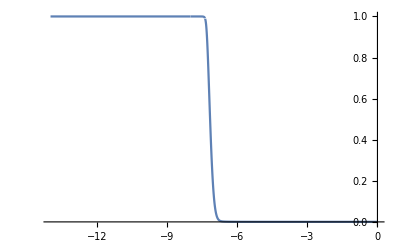

```mathematica
bxeflna=Piecewise[{{1,lna<testlnaset[[1]]},{testbxefit[lna],testlnaset[[1]]<=lna<=testlnaset[[-1]]},{bxe[lna]/.bxesol[[1]],lna>testlnaset[[-1]]}}];bxelna[lna_]=bxeflna;bganum=Exp[lna]*bxeflna*epbsollna/mhnum*sitnum/.numrep0;Plot[bxeflna,{lna,lnaini,0}]
```

```mathematica
AbsoluteTiming[npt1=1000;xsettemp=Table[lnaini+(lnaend-lnaini)/(npt1-1)*(i-1),{i,1,npt1}];ysettemp=Table[0,{i,1,npt1}];lnanpttemp=131;Do[{lna1temp,lna2temp}={xsettemp[[npt1-i]],xsettemp[[npt1-i+1]]};lnasettemp=Table[lna1temp+(lna2temp-lna1temp)/(lnanpttemp-1)*(ii-1),{ii,1,lnanpttemp}];bgasettemp=Table[bganum/calhfitlna[lna]/.lna->lnasettemp[[ii]],{ii,1,lnanpttemp}];intgtemp=Simpsonnintg[lnasettemp,bgasettemp];ysettemp[[npt1-i]]=ysettemp[[npt1-i+1]]+intgtemp,{i,1,npt1-1}]]
```

{4.42276,Null}

```mathematica
taunum=Interpolation[Table[{xsettemp[[i]],ysettemp[[i]]},{i,1,npt1}],InterpolationOrder->3,Method->"Spline"];gnum=bganum*Exp[-taunum[lna]];
```

## 5. Solve the perturbation equations numerically

```mathematica
{knummin,knummax}={0.01,1500};kcoanpt=200;knumcoaset=Table[knummin+(knummax-knummin)*(i-1)^2/(kcoanpt-1)^2,{i,1,kcoanpt}];(* knumcoaset=Table[knummin+(knummax-knummin)/(kcoanpt-1)*(i-1),{i,1,kcoanpt}]; *)lnacoanpt=4000;lna1num=-8.5;lnacoaset=Table[lna1num+(lnaend-lna1num)*(i-1)/(lnacoanpt-1),{i,1,lnacoanpt}];kpauseset={0,IntegerPart[7*kcoanpt/25],IntegerPart[11*kcoanpt/25],IntegerPart[15*kcoanpt/25],IntegerPart[19*kcoanpt/25],IntegerPart[22*kcoanpt/25],kcoanpt}
```

{0,56,88,120,152,176,200}

```mathematica
kpauseind=1;If[kpauseind==1,Export[StringJoin["bumblebee_background_data.txt"],Table[{etset[[i]],soltab[[i,1]],soltab[[i,2]],soltab[[i,3]]},{i,1,Length[etset]}],"Table"];Export[StringJoin["bumblebee_lna_data.txt"],lnacoaset,"Table"];Export[StringJoin["bumblebee_k_data.txt"],knumcoaset,"Table"];]
```

```mathematica
sourcedis1set=Table[0,{i,1,lnacoanpt},{j,1,kcoanpt}];sourcedis2set=Table[0,{i,1,lnacoanpt},{j,1,kcoanpt}];sourcedis1setpw=Table[0,{i,1,lnacoanpt},{j,1,kcoanpt}];sourcedis2setpw=Table[0,{i,1,lnacoanpt},{j,1,kcoanpt}];
```

```mathematica
labelsol=0;If[labelsol==0,{parbth00,parc1,parc4}={1,0,0}];If[labelsol==1,{parbth00,parc1,parc4}={0,1,0}];If[labelsol==4,{parbth00,parc1,parc4}={0,0,1}]
```

```mathematica
AbsoluteTiming[Do[knum=knumcoaset[[kcoai]];{bth00num,solc1,solc4}={parbth00,parc1,parc4}*Sqrt[decalrsq]/.k->knum;finhomoiniset={apphomobph,apphomobps,apphomodebt,apphomodebs}/.appinhomoini/.numrep0/.numrep1/.bth00->bth00num/.k->knum/.bt0->bt0num/.a->aininum;bthinhomoiniset={finhomoiniset[[1]]+bth00,appbth1,appbth2}/.appinhomoini/.numrep0/.numrep1/.bth00->bth00num/.k->knum/.bt0->bt0num/.a->aininum/.bga0->bxelna[lnaini]*(3*Omb0num)/(8*Pi*mhnum)*sitnum;bph0num=solc1;fhomoiniset1={apphomobph,apphomobps,apphomodebt,apphomodebs}/.apphomoini[[1]]/.bph1->bph0num/.numrep0/.numrep1/.k->knum/.bt0->bt0num/.a->aininum;bthhomoiniset1={fhomoiniset1[[1]],appbth1,appbth2}/.apphomoini[[1]]/.bph1->bph0num/.numrep0/.numrep1/.k->knum/.bt0->bt0num/.a->aininum/.bga0->bxelna[lnaini]*(3*Omb0num)/(8*Pi*mhnum)*sitnum;bph0num=solc4;fhomoiniset4={apphomobph,apphomobps,apphomodebt,apphomodebs}/.apphomoini[[3]]/.bph1->bph0num/.numrep0/.numrep1/.k->knum/.bt0->bt0num/.a->aininum;bthhomoiniset4={fhomoiniset4[[1]],appbth1,appbth2}/.apphomoini[[3]]/.bph1->bph0num/.numrep0/.numrep1/.k->knum/.bt0->bt0num/.a->aininum/.bga0->bxelna[lnaini]*(3*Omb0num)/(8*Pi*mhnum)*sitnum;finiset=finhomoiniset+fhomoiniset1+fhomoiniset4;bthiniset=bthinhomoiniset+bthhomoiniset1+bthhomoiniset4;etininum=bumetfitlna[Log[aininum]];asep1=1;parnum=2.;fpsoltrsetnum=fpsoltrset/.{calh[a]->calhsola,btf[a]->bumbtfitlna[lna],bga[a]->bganum,etf[a]->bumetfitlna[lna]}/.lna->Log[a]/.numrep0/.numrep1/.k->knum;ndsoleqset=Table[fptrset[[i]]==fpsoltrsetnum[[i]],{i,1,Length[fpsoltrset]}];ndsoliniset=Join[{bph[aininum]==finiset[[1]],bps[aininum]==finiset[[2]],debt[aininum]==finiset[[3]],debs[aininum]==finiset[[4]],deb[aininum]==3*bthiniset[[1]],dec[aininum]==3*bthiniset[[1]],vb[aininum]==-3*bthiniset[[2]],vc[aininum]==-3*bthiniset[[2]],bthf[aininum,0]==bthiniset[[1]],bthf[aininum,1]==bthiniset[[2]],bthf[aininum,2]==bthiniset[[3]]},Table[bthf[aininum,i]==0,{i,3,boln}]];ndsolfset=Join[{bph,bps,debt,debs,deb,dec,vb,vc,bthf[a,0]},Table[bthf[a,i],{i,1,boln}]];bumsol=NDSolve[{ndsoleqset,ndsoliniset},ndsolfset,{a,aininum,1},AccuracyGoal->pgnum3];{source1f1,source1f2}={gnum*(bthf[a,0]+bps[a])+Exp[-taunum[lna]]*a*calhsola*(bph'[a]+bps'[a]),-gnum*vb[a]}/.numrep0/.numrep1/.lna->Log[a]/.bumsol[[1]];Do[{sourcedis1set[[lnai,kcoai]],sourcedis2set[[lnai,kcoai]]}={source1f1,source1f2}/.a->Exp[lnacoaset[[lnai]]],{lnai,1,lnacoanpt}];If[etininum<parnum*boln/knum<etend,asep1=af[et]/.bumbgsol[[1]]/.et->parnum*boln/knum;fsep1set={bph[a],bps[a],debt[a],debs[a],deb[a],dec[a],vb[a],vc[a],bthf[a,0],bthf[a,1],bthf[a,2]}/.bumsol[[1]]/.a->asep1;sep1eqnumber=11;fpsoltrsetnum=Table[fpsoltrset[[i]]/.{bthf[a,3]->5/(k*etf[a])*bthf[a,2]-bthf[a,1]}/.{calh[a]->calhsola,btf[a]->bumbtfitlna[lna],bga[a]->bganum,etf[a]->bumetfitlna[lna]}/.lna->Log[a]/.numrep0/.numrep1/.k->knum,{i,1,sep1eqnumber}];ndsoleqset=Table[fptrset[[i]]==fpsoltrsetnum[[i]],{i,1,sep1eqnumber}];ndsoliniset={bph[asep1]==fsep1set[[1]],bps[asep1]==fsep1set[[2]],debt[asep1]==fsep1set[[3]],debs[asep1]==fsep1set[[4]],deb[asep1]==fsep1set[[5]],dec[asep1]==fsep1set[[6]],vb[asep1]==fsep1set[[7]],vc[asep1]==fsep1set[[8]],bthf[asep1,0]==fsep1set[[9]],bthf[asep1,1]==fsep1set[[10]],bthf[asep1,2]==fsep1set[[11]]};ndsolfset={bph,bps,debt,debs,deb,dec,vb,vc,bthf[a,0],bthf[a,1],bthf[a,2]};bumsep1sol=NDSolve[{ndsoleqset,ndsoliniset},ndsolfset,{a,asep1,1},PrecisionGoal->pgnum3];source1f1=Piecewise[{{gnum*(bthf[a,0]+bps[a])+Exp[-taunum[lna]]*a*calhsola*(bph'[a]+bps'[a])/.numrep0/.numrep1/.lna->Log[a]/.bumsol[[1]],a<asep1},{gnum*(bthf[a,0]+bps[a])+Exp[-taunum[lna]]*a*calhsola*(bph'[a]+bps'[a])/.numrep0/.numrep1/.lna->Log[a]/.bumsep1sol[[1]],a>=asep1}}];source1f2=Piecewise[{{-gnum*vb[a]/.numrep0/.numrep1/.lna->Log[a]/.bumsol[[1]],a<asep1},{-gnum*vb[a]/.numrep0/.numrep1/.lna->Log[a]/.bumsep1sol[[1]],a>=asep1}}]];If[parnum*boln/knum<=etininum,asep1=aininum;fsep1set={finiset[[1]],finiset[[2]],finiset[[3]],finiset[[4]],3*bthiniset[[1]],3*bthiniset[[1]],-3*bthiniset[[2]],-3*bthiniset[[2]],bthiniset[[1]],bthiniset[[2]],bthiniset[[3]]};sep1eqnumber=11;fpsoltrsetnum=Table[fpsoltrset[[i]]/.{bthf[a,3]->5/(k*etf[a])*bthf[a,2]-bthf[a,1]}/.{calh[a]->calhsola,btf[a]->bumbtfitlna[lna],bga[a]->bganum,etf[a]->bumetfitlna[lna]}/.lna->Log[a]/.numrep0/.numrep1/.k->knum,{i,1,sep1eqnumber}];ndsoleqset=Table[fptrset[[i]]==fpsoltrsetnum[[i]],{i,1,sep1eqnumber}];ndsoliniset={bph[asep1]==fsep1set[[1]],bps[asep1]==fsep1set[[2]],debt[asep1]==fsep1set[[3]],debs[asep1]==fsep1set[[4]],deb[asep1]==fsep1set[[5]],dec[asep1]==fsep1set[[6]],vb[asep1]==fsep1set[[7]],vc[asep1]==fsep1set[[8]],bthf[asep1,0]==fsep1set[[9]],bthf[asep1,1]==fsep1set[[10]],bthf[asep1,2]==fsep1set[[11]]};ndsolfset={bph,bps,debt,debs,deb,dec,vb,vc,bthf[a,0],bthf[a,1],bthf[a,2]};bumsep1sol=NDSolve[{ndsoleqset,ndsoliniset},ndsolfset,{a,asep1,1},PrecisionGoal->pgnum3];{source1f1,source1f2}={gnum*(bthf[a,0]+bps[a])+Exp[-taunum[lna]]*a*calhsola*(bph'[a]+bps'[a]),-gnum*vb[a]}/.numrep0/.numrep1/.lna->Log[a]/.bumsep1sol[[1]]];Do[{sourcedis1setpw[[lnai,kcoai]],sourcedis2setpw[[lnai,kcoai]]}={source1f1,source1f2}/.a->Exp[lnacoaset[[lnai]]],{lnai,1,lnacoanpt}];Print[{kcoai,knum,boln/knum,Log[asep1],asep1}],{kcoai,1,kcoanpt}]]
```

{1,0.01,2000.,0,1}

{2,0.0478776,417.732,0,1}

{3,0.16151,123.831,0,1}

{4,0.350898,56.9966,0,1}

{5,0.616041,32.4654,0,1}

{6,0.956939,20.9,0,1}

{7,1.37359,14.5604,0,1}

{8,1.866,10.7181,0,1}

{9,2.43417,8.21637,0,1}

{10,3.07808,6.49755,0,1}

{11,3.79776,5.26627,0,1}

{12,4.59319,4.35428,0,1}

{13,5.46437,3.66007,0,1}

{14,6.41131,3.11949,0,1}

{15,7.43401,2.69034,0,1}

{16,8.53246,2.34399,0,1}

{17,9.70666,2.06044,0,1}

{18,10.9566,1.82538,0,1}

{19,12.2823,1.62835,0,1}

{20,13.6838,1.46158,0,1}

{21,15.161,1.31917,-0.25077,0.778201}

{22,16.714,1.1966,-0.471761,0.623903}

{23,18.3427,1.09035,-0.664474,0.514544}

{24,20.0472,0.997644,-0.839347,0.431992}

{25,21.8275,0.916276,-1.00177,0.367229}

{26,23.6835,0.84447,-1.15476,0.315134}

{27,25.6152,0.780785,-1.30013,0.272496}

{28,27.6228,0.724041,-1.43907,0.237149}

{29,29.706,0.673264,-1.57238,0.207552}

{30,31.865,0.627647,-1.70065,0.182564}

{31,34.0998,0.586513,-1.82436,0.161321}

{32,36.4104,0.549294,-1.94387,0.143148}

{33,38.7966,0.515509,-2.0595,0.127518}

{34,41.2587,0.484746,-2.17151,0.114005}

{35,43.7965,0.456658,-2.28014,0.10227}

{36,46.41,0.430941,-2.38559,0.0920342}

{37,49.0993,0.407337,-2.48806,0.0830709}

{38,51.8644,0.385621,-2.58771,0.0751922}

{39,54.7052,0.365596,-2.68469,0.0682424}

{40,57.6218,0.347091,-2.77915,0.0620915}

{41,60.6141,0.329956,-2.87121,0.0566304}

{42,63.6822,0.314059,-2.961,0.0517674}

{43,66.826,0.299284,-3.04862,0.0474245}

{44,70.0456,0.285528,-3.13417,0.0435357}

{45,73.341,0.272699,-3.21777,0.0400444}

{46,76.7121,0.260715,-3.29948,0.0369025}

{47,80.159,0.249504,-3.37939,0.0340682}

{48,83.6816,0.239001,-3.45759,0.0315056}

{49,87.2799,0.229148,-3.53414,0.0291839}

{50,90.9541,0.219891,-3.60911,0.0270759}

{51,94.7039,0.211184,-3.68257,0.0251583}

{52,98.5296,0.202985,-3.75457,0.0234105}

{53,102.431,0.195253,-3.82518,0.0218146}

{54,106.408,0.187956,-3.89444,0.0203549}

{55,110.461,0.181059,-3.9624,0.0190174}

{56,114.59,0.174536,-4.02912,0.01779}

{57,118.794,0.168359,-4.09464,0.0166618}

{58,123.074,0.162504,-4.15899,0.0156233}

{59,127.43,0.156949,-4.22223,0.0146659}

{60,131.862,0.151674,-4.28439,0.0137821}

{61,136.369,0.146661,-4.3455,0.012965}

{62,140.952,0.141892,-4.4056,0.0122088}

{63,145.611,0.137352,-4.46473,0.0115078}

{64,150.346,0.133026,-4.52291,0.0108574}

{65,155.157,0.128902,-4.58017,0.0102532}

{66,160.043,0.124967,-4.63654,0.00969113}

{67,165.005,0.121209,-4.69206,0.00916779}

{68,170.042,0.117618,-4.74674,0.00867995}

{69,175.156,0.114184,-4.80061,0.00822474}

{70,180.345,0.110898,-4.85369,0.00779952}

{71,185.61,0.107753,-4.90601,0.00740195}

{72,190.951,0.104739,-4.95759,0.00702985}

{73,196.367,0.10185,-5.00845,0.00668127}

{74,201.86,0.0990788,-5.0586,0.00635444}

{75,207.428,0.0964192,-5.10807,0.00604772}

{76,213.071,0.0938653,-5.15688,0.00575963}

{77,218.791,0.0914115,-5.20505,0.0054888}

{78,224.586,0.0890527,-5.25258,0.00523401}

{79,230.457,0.086784,-5.2995,0.0049941}

{80,236.404,0.0846009,-5.34582,0.00476804}

{81,242.427,0.0824992,-5.39156,0.00455487}

{82,248.525,0.0804749,-5.43673,0.0043537}

{83,254.699,0.0785241,-5.48135,0.00416372}

{84,260.949,0.0766434,-5.52542,0.00398419}

{85,267.274,0.0748295,-5.56897,0.00381441}

{86,273.676,0.0730792,-5.612,0.00365375}

{87,280.153,0.0713897,-5.65453,0.00350161}

{88,286.705,0.069758,-5.69657,0.00335746}

{89,293.334,0.0681817,-5.73813,0.00322079}

{90,300.038,0.0666582,-5.77922,0.00309114}

{91,306.818,0.0651851,-5.81984,0.00296807}

{92,313.674,0.0637604,-5.86002,0.00285118}

{93,320.606,0.0623819,-5.89976,0.00274009}

{94,327.613,0.0610476,-5.93908,0.00263446}

{95,334.696,0.0597557,-5.97797,0.00253397}

{96,341.855,0.0585043,-6.01645,0.00243832}

{97,349.09,0.0572919,-6.05452,0.00234722}

{98,356.4,0.0561167,-6.0922,0.00226042}

{99,363.786,0.0549773,-6.1295,0.00217767}

{100,371.248,0.0538723,-6.16642,0.00209874}

{101,378.786,0.0528003,-6.20296,0.00202343}

{102,386.399,0.0517599,-6.23914,0.00195153}

{103,394.088,0.05075,-6.27497,0.00188285}

{104,401.853,0.0497694,-6.31045,0.00181722}

{105,409.694,0.0488169,-6.34558,0.00175449}

{106,417.61,0.0478915,-6.38038,0.00169449}

{107,425.602,0.0469922,-6.41484,0.00163708}

{108,433.67,0.046118,-6.44899,0.00158212}

{109,441.814,0.0452679,-6.48281,0.0015295}

{110,450.034,0.0444411,-6.51633,0.00147909}

{111,458.329,0.0436368,-6.54954,0.00143078}

{112,466.7,0.0428541,-6.58244,0.00138446}

{113,475.146,0.0420923,-6.61506,0.00134004}

{114,483.669,0.0413506,-6.64738,0.00129742}

{115,492.267,0.0406284,-6.67942,0.00125651}

{116,500.941,0.0399249,-6.71118,0.00121723}

{117,509.691,0.0392395,-6.74266,0.00117951}

{118,518.516,0.0385716,-6.77387,0.00114326}

{119,527.417,0.0379206,-6.80482,0.00110842}

{120,536.394,0.037286,-6.8355,0.00107492}

{121,545.447,0.0366672,-6.86593,0.00104271}

{122,554.576,0.0360636,-6.89611,0.00101171}

{123,563.78,0.0354748,-6.92604,0.000981882}

{124,573.06,0.0349004,-6.95572,0.000953164}

{125,582.416,0.0343397,-6.98517,0.000925508}

{126,591.847,0.0337925,-7.01438,0.000898867}

{127,601.354,0.0332583,-7.04335,0.000873197}

{128,610.937,0.0327366,-7.0721,0.000848453}

{129,620.596,0.0322271,-7.10062,0.000824597}

{130,630.331,0.0317294,-7.12891,0.00080159}

{131,640.141,0.0312431,-7.15699,0.000779394}

{132,650.027,0.0307679,-7.18486,0.000757977}

{133,659.989,0.0303035,-7.21251,0.000737304}

{134,670.026,0.0298496,-7.23995,0.000717344}

{135,680.14,0.0294057,-7.26719,0.000698069}

{136,690.329,0.0289717,-7.29423,0.000679449}

{137,700.594,0.0285472,-7.32107,0.000661457}

{138,710.934,0.028132,-7.3477,0.000644069}

{139,721.351,0.0277258,-7.37415,0.000627259}

{140,731.843,0.0273283,-7.40041,0.000611005}

{141,742.411,0.0269393,-7.42647,0.000595283}

{142,753.054,0.0265585,-7.45235,0.000580074}

{143,763.773,0.0261858,-7.47805,0.000565357}

{144,774.569,0.0258208,-7.50357,0.000551113}

{145,785.439,0.0254635,-7.52891,0.000537323}

{146,796.386,0.0251134,-7.55408,0.00052397}

{147,807.408,0.0247706,-7.57907,0.000511037}

{148,818.507,0.0244347,-7.60389,0.000498509}

{149,829.68,0.0241057,-7.62854,0.000486369}

{150,840.93,0.0237832,-7.65303,0.000474604}

{151,852.256,0.0234671,-7.67735,0.0004632}

{152,863.657,0.0231574,-7.70151,0.000452142}

{153,875.134,0.0228537,-7.72552,0.000441419}

{154,886.686,0.0225559,-7.74936,0.000431018}

{155,898.315,0.0222639,-7.77305,0.000420927}

{156,910.019,0.0219776,-7.79659,0.000411136}

{157,921.799,0.0216967,-7.81997,0.000401633}

{158,933.654,0.0214212,-7.84321,0.000392409}

{159,945.586,0.0211509,-7.86629,0.000383452}

{160,957.593,0.0208857,-7.88924,0.000374755}

{161,969.676,0.0206254,-7.91204,0.000366308}

{162,981.835,0.02037,-7.93469,0.000358102}

{163,994.069,0.0201193,-7.95721,0.000350129}

{164,1006.38,0.0198732,-7.97959,0.000342381}

{165,1018.77,0.0196316,-8.00183,0.000334851}

{166,1031.23,0.0193944,-8.02393,0.00032753}

{167,1043.76,0.0191614,-8.0459,0.000320412}

{168,1056.38,0.0189326,-8.06774,0.00031349}

{169,1069.07,0.0187079,-8.08945,0.000306758}

{170,1081.83,0.0184872,-8.11103,0.000300209}

{171,1094.67,0.0182703,-8.13249,0.000293837}

{172,1107.59,0.0180573,-8.15381,0.000287636}

{173,1120.58,0.0178479,-8.17502,0.000281602}

{174,1133.65,0.0176422,-8.1961,0.000275728}

{175,1146.79,0.01744,-8.21706,0.000270009}

{176,1160.01,0.0172412,-8.23789,0.000264441}

{177,1173.31,0.0170459,-8.25861,0.000259018}

{178,1186.68,0.0168538,-8.27922,0.000253736}

{179,1200.12,0.016665,-8.2997,0.000248591}

{180,1213.65,0.0164793,-8.32007,0.000243578}

{181,1227.24,0.0162967,-8.34033,0.000238693}

{182,1240.92,0.0161171,-8.36048,0.000233932}

{183,1254.67,0.0159405,-8.38051,0.000229292}

{184,1268.49,0.0157668,-8.40044,0.000224769}

{185,1282.39,0.0155958,-8.42026,0.000220358}

{186,1296.37,0.0154277,-8.43996,0.000216058}

{187,1310.42,0.0152623,-8.45957,0.000211864}

{188,1324.55,0.0150995,-8.47907,0.000207773}

{189,1338.76,0.0149393,-8.49846,0.000203782}

{190,1353.03,0.0147816,-8.51775,0.000199889}

{191,1367.39,0.0146264,-8.53694,0.00019609}

{192,1381.82,0.0144736,-8.55603,0.000192382}

{193,1396.33,0.0143233,-8.57502,0.000188763}

{194,1410.91,0.0141752,-8.59391,0.000185231}

{195,1425.57,0.0140295,-8.6127,0.000181783}

{196,1440.3,0.0138859,-8.63139,0.000178416}

{197,1455.12,0.0137446,-8.64999,0.000175128}

{198,1470.,0.0136054,-8.6685,0.000171917}

{199,1484.96,0.0134684,-8.68691,0.00016878}

{200,1500.,0.0133333,-8.70523,0.000165717}

{2346.44,Null}

```mathematica
AbsoluteTiming[Export[StringJoin["bumblebee_sourcedis1set_data.txt"],sourcedis1set,"Table"];Export[StringJoin["bumblebee_sourcedis2set_data.txt"],sourcedis2set,"Table"];]
```

{31.7134,Null}

## 6. Print total time used

```mathematica
Print["End: ",TimeUsed[]]
```

End: 4129.28